# Building WolframCloud APIs for JavaScript (React, Node, AWS) Livecoding Session 3

## Initializations

https://www.wolframcloud.com/
https://datadrop.wolframcloud.com/

```mathematica
$CloudBase="https://www.wolframcloud.com/"
```

https://www.wolframcloud.com/

```mathematica
CloudConnect["...your account email..."]
```

mitch@aitoconsulting.com

```mathematica
ClearAll[choices,get]
choices=Sort[{"posts","comments","albums","photos","todos","users"}]
get[it_String]:=Import["https://jsonplaceholder.typicode.com/"<>it,"RawJSON"]
```

{albums,comments,photos,posts,todos,users}

## Overview

Assumptions:
- Familiarity with Mathematica.  
- Familiarity of JS is helpful but not required for this presentation.

A few words about:
- Introduction and background for React (https://reactjs.org/) / Axios and Node (https://nodejs.org/en/) / Express.
- Wolfram setup, we will use the following tools:
	- Mathematica desktop (wolfram.com/) & Wolfram Cloud (wolframcloud.com - free sign up.  You can use Wolfram Cloud (WC) alone if you like)
- Other than Wolfram setup:
	- npm (https://www.npmjs.com/) 
	- git (https://git-scm.com/)
	- GitHub (https://github.com/)
	- AWS (free tier: https://aws.amazon.com/console/)
	- AWS-CLI (https://aws.amazon.com/cli/)
	- AWS Amplify (https://aws.amazon.com/amplify/)
	- create-react-app (https://facebook.github.io/create-react-app/)
	- Chrome browser (google.com/chrome).  We will use chrome developer tools.  Other browsers and their browser tools may not be sufficient for what we will doing)
	- Postman (getpostman.com/ for validating and testing APIs)

## Introduction

Motivating principle: separation of duties for people and software supporting the goals of modular design principles.  Easy to understand separating people by expertise in front-end, back-end and quantitative capabilities and code production.

This is the first of three (or more) live-coding walk-through’s that show an approach to integrating Mathematica to a browser front-end (ReactJS) and a serverless back-end (Node JS and AWS).

ReactJS is a JavaScript (JS) library widely used to make single page applications (SPAs).   ‘Hooks’ were introduced in the recently released version 16.8 (https://reactjs.org/docs/hooks-intro.html).  Using hooks allows React developers to write JS applications using 100% functional methods - eliminating the need for JS classes.  There are many advantages to this new capability and we will focus on the implications for APIs between React and the Wolfram Cloud (WC) and between AWS and WC.

We will show JS and JSX (https://reactjs.org/docs/introducing-jsx.html) with respect to how the API requests (req) and responses (res) are managed.  The JS browser app is a bear bones deployment with minimal styling and organization considerations.  

We will iterate from the simplest possible API (that I can think of) to ever more complex patterns.  There are JS and React considerations that impact the WC side of the API.  A number of these considerations will be presented, discussed and dealt with.  In every instance the goal is to produce Mathematica side code that is simultaneously used for presentation in a browser and analytical use is Mathematica. 

Some requests and considerations:
- You will see the URL I use (my WC account) and API end-points I am using.  I've made these public for these live coding sessions.  It's ok during the live coding session to use my APIs if you can't make yours work, but please setup your own WC account, make your own APIs and use them.

The general development pattern:
1.0) Three parts to APIFunction[...]:
	1.1) inputs
	1.2) functions
	1.3) output format
2.0) Test by passing an association of API inputs <|key -> value, ...|>
3.0) Two’ish parts to CloudDeploy[...]:
	3.1) the api function (1 above)
	3.2) options:
		3.2.1) the path and api name
		3.2.2) permissions
4.0) Test:
	4.1) to a browser with StartWebSession[...] and WebExecute[...]
	4.2) to postman
5.0) Connect to:
	5.1) front-end (React)
	5.2) backend (Node)
		5.2.1) test serverless api between AWS (via Node) and WC 

Here are a couple web sites that are built on this pattern where the front-end is a Single Page Application (SPA) using React, the back-end is serverless and built on NodeJS - AWS, and everything computational is done with Wolfram (Wolfram Cloud):
	- https://www.aitoconsulting.org/options-pub
	- https://www.christyhealth.org/

## Build your own API maker functions : v01

```mathematica
ClearAll[makeAPI,args,func,frmt]
makeAPI[args_List, func_Function,frmt_String]:= APIFunction[
args,
func,
 frmt
];

ClearAll[makeCD,args,func,frmt]
makeCD[args_List, func_Function,frmt_String,endPoint_String,funcName_String,permit_String]:=CloudDeploy[
makeAPI[args, func,frmt],
"/"<>endPoint<>"/"<>funcName<>"/",
Permissions->"Public"
];
```

```mathematica
ClearAll[args,func,frmt,params]
args={"x"->Interpreter["Integer"],"y"->Interpreter["Integer"]};
func=Function[ RandomInteger[{#x,#y}] ];
frmt="JSON";

params=<|"x"->-10,"y"->10|>;
makeAPI[args, func,frmt][params]
```

2

```mathematica
endPoint="live-coding-unitTest";
funcName="random-integer";
permit="Public";

makeCD[args, func,frmt,endPoint,funcName,permit]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding-unitTest/random-integer]

#### Test 1

```mathematica
ClearAll[url,session]

url=URLBuild[ makeCD[args, func,frmt,endPoint,funcName,permit],params ]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding-unitTest/random-integer?x=-10&y=10

#### Test 2

```mathematica
ClearAll[args,func,frmt,params,endPoint,funcName,url,session]

args={"a"->Interpreter["Integer"],"b"->Interpreter["Integer"]};
func=Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between "<>ToString[#a]<>" and "<>ToString[#b]<>" in "<>frmt<>" Format"],12,Black,Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Blue},
PlotLegends->"Expressions",
Epilog->Flatten[{PointSize[0.015],Point[{#*Pi,0}]&/@Range[#a,#b,.5]}],
ImageSize->Medium]
];
frmt="SVG";
params=<|"a"->-3,"b"->3|>;

endPoint="live-coding-unitTest";
funcName="sin-"<>ToLowerCase[frmt];
permit="Public";

url=URLBuild[makeCD[args, func,frmt,endPoint,funcName,permit],params]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding-unitTest/sin-svg?a=-3&b=3

## API-9) Images - Get external data and make geo image

Using the makeAPI functions

```mathematica
ClearAll[it,n,locations]
(* aurguments *)
it="users";
n=All;
(* function *)
locations=GeoPosition[ToExpression[#]]&/@Normal[Dataset[get[it]][n,"address","geo",{"lat","lng"}/*Values]];
GeoGraphics[{{
Blue,
GeoPath[locations,"Geodesic"],
GeoMarker[locations]
}},
GeoRange->"World",GeoProjection->"Robinson"]
```

-Graphics-

```mathematica
"All"//Head
ToExpression["All"]//Head
```

String

Symbol

```mathematica
ClearAll[args,func,frmt,params,endPoint,funcName,url,session]

args={"it"->"String","n"->"String"};
func=Function[
locations=GeoPosition[ToExpression[#]]&/@Normal[Dataset[get[#it]][ToExpression[n],"address","geo",{"lat","lng"}/*Values]];
GeoGraphics[{{
Blue,
GeoPath[locations,"Geodesic"],
GeoMarker[locations]
}},
GeoRange->"World",GeoProjection->"Robinson"]
];
frmt="PNG";
params=<|"it"->"users","n"->"All"|>;
makeAPI[args, func,frmt][params]
```

-Graphics-

```mathematica
ClearAll[endPoint,funcName,permit,url,session]
endPoint="live-coding";
funcName="geo-pins";
permit="Public";

url=URLBuild[makeCD[args, func,frmt,endPoint,funcName,permit],params]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/geo-pins?it=users&n=All

#### Execute the API build block

```mathematica
ClearAll[args,func,frmt,params,endPoint,funcName,url,session]

args={"it"->"String","n"->"String"};
func=Function[
locations=GeoPosition[ToExpression[#]]&/@Normal[Dataset[get[#it]][ToExpression[n],"address","geo",{"lat","lng"}/*Values]];
GeoGraphics[{{
Blue,
GeoPath[locations,"Geodesic"],
GeoMarker[locations]
}},
GeoRange->"World",GeoProjection->"Robinson"]
];
frmt="PNG";
params=<|"it"->"users","n"->"All"|>;
endPoint="live-coding";
funcName="geo-pins";
permit="Public";

url=URLBuild[makeCD[args, func,frmt,endPoint,funcName,permit],params]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/geo-pins?it=users&n=All

## API - 10) Images - Getting size and aspect ratio ‘right’

## Tips & tricks when it comes to ‘fitting’ a WL image into a defined html ‘image space’ with required aspect ratio.

Managing the dimensions of images between what is produced by WL and what is available/required in the HTML can seem daunting on the first attempt.  I will review the steps I go through to meet my needs - almost - every time.  First, I’ve found a few common scenarios keep recurring.  These are:
- Graphics
	- Graphics[ primitives ] : represents a two-dimensional graphical image. 
- Images 
	- Image[ graphics ] : creates a raster image from a graphics object.
	- Image[ data ] : represents a raster image with pixel values given by the array data.

There are 3 options that will be our friends through this process:
1) ImageSize
2) AspectRatio 
3) RasterSize

What is image size?
ImageSize: (from help)
d | d printer's points (before magnification) 
72di | di inches (before magnification) 
(Wolfram documentation)
Common measurement units:
- dots per inch (dpi)
- pixels per inch (ppi)
- bits per pixel (bpp)
(https://en.wikipedia.org/wiki/Pixel)

What is aspect ratio? 
The aspect ratio of an element describes the proportional relationship between its width and its height. Two common video aspect ratios are 4:3 (the universal video format of the 20th century), and 16:9 (universal for HD television and European digital television).
(https://www.w3schools.com/howto/howto_css_aspect_ratio.asp)

We can use the h and w in a unit-less relationship.  Most common aspect ratios:
w:h    → h/w→ approximate real → percent
In Mathematica terms:
x:y    → y/x→ approximate real → percent
Examples:
21:9 → 9/21→ 0.4285 → 42.85%
16:9 → 9/16→ 0.5625 → 56.25%
4:3 → 3/4→ 0.75 → 75.0%
1:1 → 1/1→ 1.0 → 100.0%

What we want to do is dimension the WL output for the allocated HTML ‘image container’.  
<img src=”html5.gif” alt=”HTML5 Icon” width=”128” height=”128”>
<img src=”html5.gif” alt=”HTML5 Icon” style=”width:128px;height:128px;”>
(https://www.w3schools.com/html/html_images.asp)

Combine size dimension units: 
We’ll start with a simple Plot then work our way to controlling the aspect ratio and size.  We get ourselves in the position of having (or wanting) one dimension (h or w) and wanting to know the other (w or h).

Let’s play with this a little...

#### Step 1

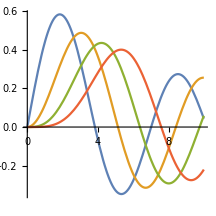

Graphics

{{216,195},65/72,0.902778}

```mathematica
ClearAll[plt,di,ndi]
di=72;
ndi=3;

plt=Plot[
Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},
ImageSize->di*ndi,
AspectRatio->1
];
Framed[plt
,FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray
]
plt//Head
{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

#### Step 2

Relationship between:
- ImageSize: is an option that specifies the overall size of an image to display for an object.
and 
- AspectRatio: is an option for Graphics and related functions that specifies the ratio of height to width for a plot.

Make the params for ImageSize and AspectRatio then try removing one then the other to see what happens

```mathematica
ClearAll[plt,di,ndi,xBasePX,yBasePX,basePX,xAR,yAR,xPX,yPX]
di=72;
ndi=3;
xAR=1;
yAR=1;

xPX=di*ndi
yPX=xPX*(yAR/xAR)//N
```

216

216.

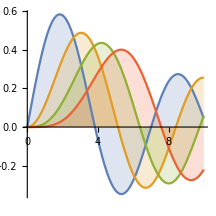

{{216,216},1,1.}

```mathematica
ClearAll[plt]
plt=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,
ImageSize->{xPX,yPX},
AspectRatio->yPX/xPX
];
Framed[plt,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray]
{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

#### Step 3

We can use our aspect ratio to scale our unknown image size parameter.  You only need to know the x or y size dimension.

```mathematica
ClearAll[wPX,hPX]
(* bp = base (or known) pixels of either x (w) or y (h) *)
wPX[base_]:=base
wPX[base_,w_,h_]:=base*(w/h)
hPX[base_]:=base
hPX[base_,w_,h_]:=base*(h/w)
```

```mathematica
bpW=72*2;
wPX[bpW]
hPX[bpW,16,9]
%/%%
```

144

81

9/16

```mathematica
bpH=72*2;
wPX[bpH,16,9]
hPX[bpH]
%/%%
```

256

144

9/16

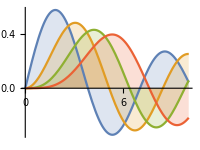

{{200,150},3/4,0.75}

```mathematica
ClearAll[plt,bp,bpW,bpH,w,h]
bpW=200;
w=4;
h=3;

ClearAll[plt]
plt=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
AspectRatio->hPX[bpW,w,h]/wPX[bpW]
];
Framed[plt]
{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

#### Step 4

OK so far!  Now we need to add all sorts of goodies to out graphics like legends, labels, frame, axes labels and ticks and on and on...

Now let see what happens when we decrease the size... we will need to style the font size down.

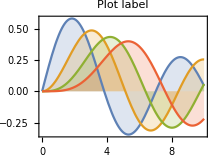

{{216,162},3/4,0.75}

```mathematica
ClearAll[plt,bp,bpW,bpH,w,h]
bpW=72*3;
w=4;
h=3;

plt=
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},
Filling->Axis,
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
AspectRatio->hPX[bpW,w,h]/wPX[bpW],
PlotLabel->Style["Plot label",9],
(*PlotLegends->Placed[{"1","2","3","4"},Below],*) 
Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Blue,8],
FrameLabel->{Style[#,8]&/@{"y on left","y on right"},Style[#,8]&/@{"x on bottom","x on top"}}
];
Framed[plt,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->LightRed]
{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

On to Images...

So far we’ve seen how to control and size and aspect ratio of graphics.  How about images made from arbitrary stuff like equations, tables, grids and so on?

Make an equation:

```mathematica
ClearAll[equ]
equ=1+a x^2+√((b y^3)/(a+x))
equ//Head
equ//FullForm
```

1+a x^2+√((b y^3)/(a+x))

Plus

Plus[1,Times[a,Power[x,2]],Power[Times[b,Power[Plus[a,x],-1],Power[y,3]],Rational[1,2]]]

Frame the equation to see the area WL gives the equation automatically.

```mathematica
Framed[
equ,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->LightRed
]
```

1+a x^2+√((b y^3)/(a+x))

```mathematica
ClearAll[rstr]
rstr=Rasterize[
Framed[
equ,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->LightRed
]
]
rstr//Head
{ImageDimensions[rstr],ImageAspectRatio[rstr],N@ImageAspectRatio[rstr]}
```

-Graphics-

Image

{{111,43},43/111,0.387387}

Rasterize[ ] and it’s option RasterSize:
The option for Rasterizepaclet:ref/Rasterize and related functions that determines the absolute pixel size of the raster generated.
w | width w pixels
{w,h} | explicit pixel width and height 
{{w_max},{h_max}} | pixel width and height maximums
{{w_min,w_max},{h_min,h_max}} | pixel width and height ranges
(Wolfram documentation)

Note the use of Framed so that we can use the option, ImageSize!

Play with rsMult, you will notice:
- as rsMult goes from 1 to n aspect ratio converges and ImageDimensions (gives the pixel dimensions of an image) increases.  
- the overlap of the raster area and the frame border at various increments 
- as the ImageDimensions -> screen resolution (my screen: 1920 x 1020) clarity/crispness improves.

```mathematica
ClearAll[rstr,bpW,w,h,fs,rsMult]
bpW=72*2;
w=16;
h=9;
fs=12;
rsMult=13;

rstr=Rasterize[
Framed[
Item[Style[equ,FontFamily->"Arabic Transparent",FontSize->fs],Alignment->{Center,Center}],
(*equ*)
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
(*RoundingRadius->10,*)
FrameStyle->Directive[Red,Thickness[1]]
],
RasterSize->rsMult*bpW,
Background->LightYellow
]
rstr//Head
{ImageDimensions[rstr],ImageAspectRatio[rstr],N@ImageAspectRatio[rstr]}
```

-Graphics-

Image

{{1872,1055},1055/1872,0.563568}

#### Graphic and Image options of interest

```mathematica
?ImageSize
```

```mathematica
?FrameMargins
```

```mathematica
?ImageMargins
```

```mathematica
?ImageDimensions
```

```mathematica
?ImageAspectRatio
```

ImageResolutionpaclet:ref/ImageResolution->r specifies that a bitmap should be rendered at a resolution of r dpi. 
ImageResolutionpaclet:ref/ImageResolution is relevant only for bitmap graphics formats such as “PGN”, and not for resolution-independent formats such as “SVG”.

RaserSize overrides.

```mathematica
?ImageResolution
```

Graphics

```mathematica
?AspectRatio
```

```mathematica
?BoxRatios (* for 3D graphics *)
```

Grids

```mathematica
?Spacings
```

```mathematica
?ItemSize
```

### Back to making APIs (for <img /> tags)

With the basics out of the way let’s get back to making APIs.  We’ll use Solve[ ] to produce a couple equations then make an image of the result and return it via an API.

```mathematica
ClearAll[eq]
eq=Solve[x^2+a x+1==0,x];
eq
eq//Head
eq//FullForm
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

List

List[List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Times[-1,Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]],List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]]

```mathematica
eq[[1,1,1]]
```

x

```mathematica
{Text[Style[#,Black,Italic,24]]}&/@Flatten[eq]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

We use Grid to have access to each ‘cell’ and the spacing and styles for each, as needed.
Must use Framed[ ] to have access to ImageSize.

```mathematica
ClearAll[grd,frmd,rstr,bpW,w,h,xL,xR,yT,yC,yB,fs,rsMult]
xL=0;
xR=0;
yT=0;
yC=1;
yB=0;
bpW=200;(*base pixels width*)
w=16;
h=9;
fs=17.5;(*font size*)
rsMult=9;(*RasterSize multipule*)

grd=Grid[
{Text[Style[#,Black,fs]]}&/@Flatten[eq],
Spacings->{{xL,xR},{yT,yC,yB}},
Frame->All,
FrameStyle->Directive[Red,Dashed,Thickness[1]]
]

frmd=Framed[
Item[
Style[
grd,
FontFamily->"Arabic Transparent",FontSize->fs
],
Alignment->{Center,Center}
],
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
RoundingRadius->0,
FrameStyle->Red
]

rstr=Rasterize[
frmd,
(* must include ImageSize here.  try changing bpW to see why.  *)
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
RasterSize->rsMult*bpW
]

grd//Head
frmd//Head
rstr//Head

{ImageDimensions[rstr],ImageAspectRatio[rstr],N@ImageAspectRatio[rstr]}
```

x→1/2 (-a-√(-4+a^2))
x→1/2 (-a+√(-4+a^2))

x→1/2 (-a-√(-4+a^2))
x→1/2 (-a+√(-4+a^2))

-Graphics-

Grid

Framed

Image

{{1800,1015},203/360,0.563889}